```mathematica
{0,1,2,3}
!{{0,1},{1,2},{2,3},{3,0}}
"no i -> i+1";
"no repeats";
"no i -> i";

1,0,r
1,1,s
1,2,c
1,3,
```

```mathematica
FullSimplify[n(n-1)/2-n]
```

1/2 (-3+n) n

```mathematica
numchords[m_]:=1/2 (-3+m) m
```

```mathematica
m=4;
allpairs=Flatten[Table[{j,i},{j,0,m-1},{i,j+1,m-1}],1]
```

{{0,1},{0,2},{0,3},{1,2},{1,3},{2,3}}

```mathematica
(*not in original cycle*)
undirchords=Select[allpairs,(Mod[#[[1]]-#[[2]],m]≠1)&&(Mod[#[[2]]-#[[1]],m]≠1)&]
```

{{0,2},{1,3}}

```mathematica
Map[Mod[#-1,3]&,{0,1,2}]
```

{2,0,1}

```mathematica
chords=Map[If[antipar[0,#],Reverse[#],#]&,undirchords]
```

{{2,0},{3,1}}

```mathematica
Table[Boole[antipar[x,chords[[i]]]],{x,0,m-1},{i,1,numchords[m]}]
```

{{0,0},{1,0},{1,1},{0,1}}

```mathematica
Clear[antipar]
```

```mathematica
numchords[m_]:=1/2 (-3+m) m
antipar[m0_,x_,{a_,b_}]:=Mod[a-x,m0]<Mod[b-x,m0]

sumat[m_]:=
Monitor[Block[{allpairs=Flatten[Table[{j,i},{j,0,m-1},{i,j+1,m-1}],1]},
Block[{undirchords=Select[allpairs,(Mod[#[[1]]-#[[2]],m]≠1)&&(Mod[#[[2]]-#[[1]],m]≠1)&]},
Block[{chords=Map[If[antipar[m,0,#],Reverse[#],#]&,undirchords]},
Table[Boole[antipar[m,k,chords[[l]]]],{k,0,m-1},{l,1,numchords[m]}]]]],{k,l,j,i}]
```

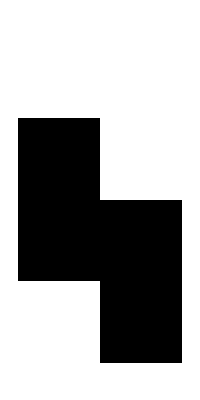

```mathematica
ArrayPlot[sumat[4]]
```

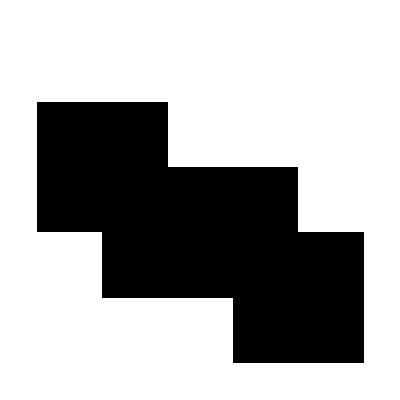

```mathematica
ArrayPlot[sumat[5]]
```

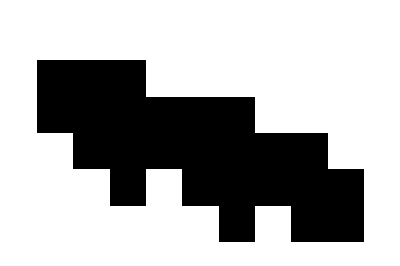

```mathematica
ArrayPlot[sumat[6]]
```

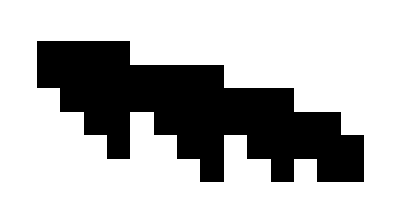
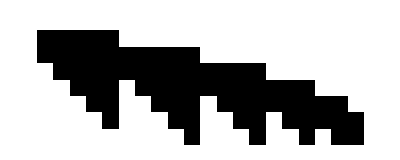
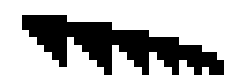
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[sumat[i]],{i,4,10}]
```

```mathematica
xordif[l_]:=Table[BitXor[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

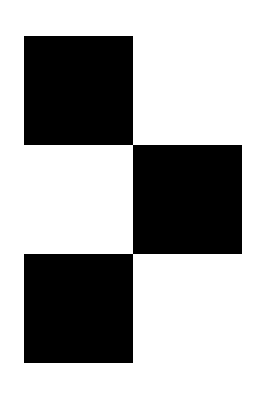
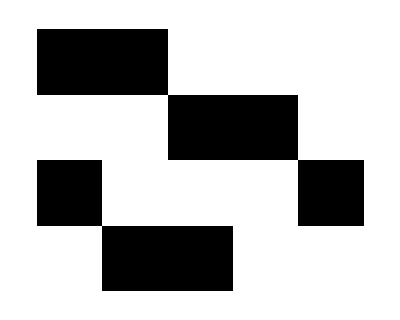
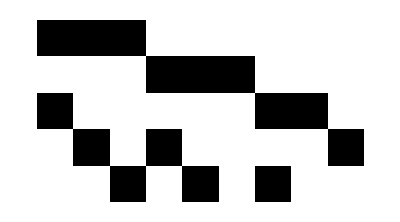
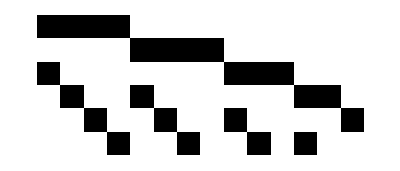
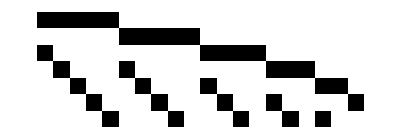
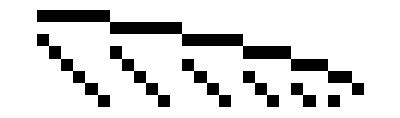
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[xordif[sumat[i]]],{i,4,10}]
```

```mathematica
Table[xordif[sumat[i]],{i,4,4}]
```

{{{1,0},{0,1},{1,0}}}

```mathematica
First[%]
```

{{1,0},{0,1},{1,0}}

```mathematica
Map[Flatten[Position[#,1]]&,%]
```

{{1},{2},{1}}

```mathematica
onef[x_]:=Map[Flatten[Position[#,1]]&,x]
```

```mathematica
Map[onef,Table[xordif[sumat[i]],{i,4,7}]]//Column
```

{{1},{2},{1}}
{{1,2},{3,4},{1,5},{2,3}}
{{1,2,3},{4,5,6},{1,7,8},{2,4,9},{3,5,7}}
{{1,2,3,4},{5,6,7,8},{1,9,10,11},{2,5,12,13},{3,6,9,14},{4,7,10,12}}

```mathematica
anddif[l_]:=Table[BitAnd[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

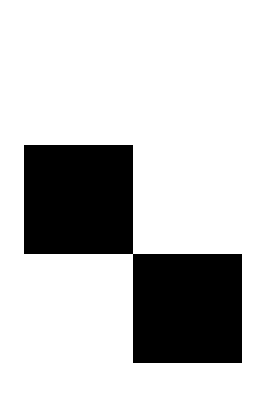
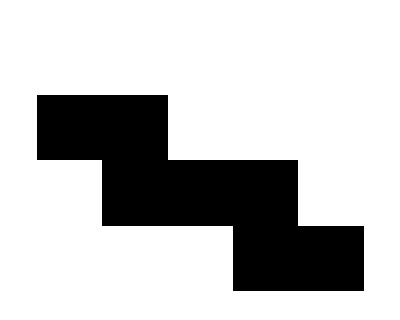
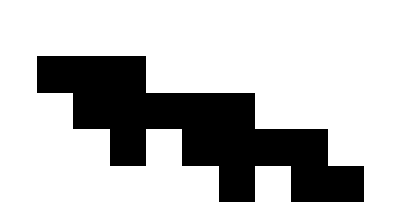
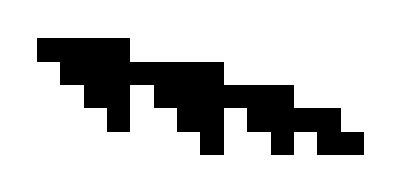
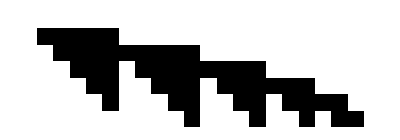
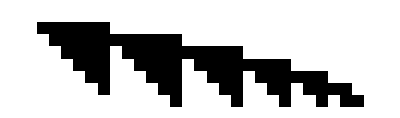
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[anddif[sumat[i]]],{i,4,10}]
```

```mathematica
ordif[l_]:=Table[BitOr[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

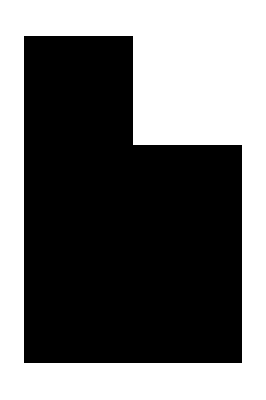
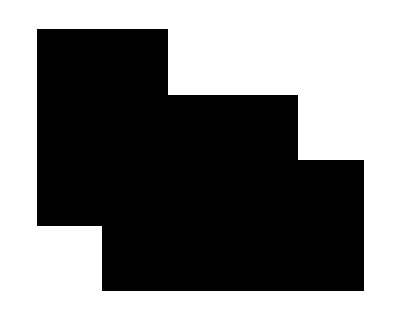
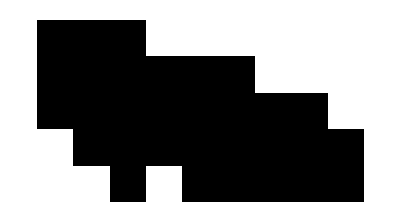
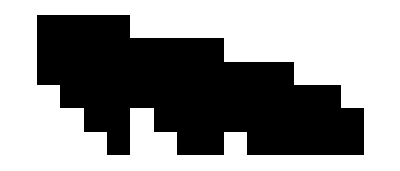
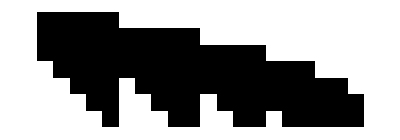
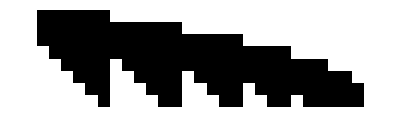
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[ordif[sumat[i]]],{i,4,10}]
```

```mathematica
hamdif[l_]:=Table[HammingDistance[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

```mathematica
hamdif[sumat[4]]
```

{1,1,1}

```mathematica
Table[hamdif[sumat[i]],{i,4,10}]
```

{{1,1,1},{2,2,2,2},{3,3,3,3,3},{4,4,4,4,4,4},{5,5,5,5,5,5,5},{6,6,6,6,6,6,6,6},{7,7,7,7,7,7,7,7,7}}

```mathematica
xvar[i_]:=ToExpression[StringJoin["x",ToString[i]]]
```

```mathematica
sumat[4]
```

{{0,0},{1,0},{1,1},{0,1}}

```mathematica
tooneform[l_]:=1≤Sum[If[l[[i]]==1,xvar[i],1-xvar[i]],{i,1,Length[l]}]
```

```mathematica
Map[tooneform,sumat[4]]
```

{1≤2-x1-x2,1≤1+x1-x2,1≤x1+x2,1≤1-x1+x2}

```mathematica
Join[%,Table[0≤xvar[i]≤1,{i,1,2}]]
```

{1≤2-x1-x2,1≤1+x1-x2,1≤x1+x2,1≤1-x1+x2,0≤x1≤1,0≤x2≤1}

```mathematica
Reduce[%,Integers]
```

False

```mathematica
tots=Table[DeleteDuplicates[Sort[Map[Total,sumat[i]]]],{i,4,20}];
Column[tots]
```

{0,1,2}
{0,2,4}
{0,3,6,7}
{0,4,8,10}
{0,5,10,13,14}
{0,6,12,16,18}
{0,7,14,19,22,23}
{0,8,16,22,26,28}
{0,9,18,25,30,33,34}
{0,10,20,28,34,38,40}
{0,11,22,31,38,43,46,47}
{0,12,24,34,42,48,52,54}
{0,13,26,37,46,53,58,61,62}
{0,14,28,40,50,58,64,68,70}
{0,15,30,43,54,63,70,75,78,79}
{0,16,32,46,58,68,76,82,86,88}
{0,17,34,49,62,73,82,89,94,97,98}

```mathematica
Map[PadRight[Drop[#,1],10]&,tots]//TableForm
```

1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 6 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 8 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 10 | 13 | 14 | 0 | 0 | 0 | 0 | 0 | 0
6 | 12 | 16 | 18 | 0 | 0 | 0 | 0 | 0 | 0
7 | 14 | 19 | 22 | 23 | 0 | 0 | 0 | 0 | 0
8 | 16 | 22 | 26 | 28 | 0 | 0 | 0 | 0 | 0
9 | 18 | 25 | 30 | 33 | 34 | 0 | 0 | 0 | 0
10 | 20 | 28 | 34 | 38 | 40 | 0 | 0 | 0 | 0
11 | 22 | 31 | 38 | 43 | 46 | 47 | 0 | 0 | 0
12 | 24 | 34 | 42 | 48 | 52 | 54 | 0 | 0 | 0
13 | 26 | 37 | 46 | 53 | 58 | 61 | 62 | 0 | 0
14 | 28 | 40 | 50 | 58 | 64 | 68 | 70 | 0 | 0
15 | 30 | 43 | 54 | 63 | 70 | 75 | 78 | 79 | 0
16 | 32 | 46 | 58 | 68 | 76 | 82 | 86 | 88 | 0
17 | 34 | 49 | 62 | 73 | 82 | 89 | 94 | 97 | 98

```mathematica
1,2,3,4,5,6
```

```mathematica
Map[PadRight[Drop[#,1],10]&,tots]//MatrixForm
```

(1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 6 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 8 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 10 | 13 | 14 | 0 | 0 | 0 | 0 | 0 | 0
6 | 12 | 16 | 18 | 0 | 0 | 0 | 0 | 0 | 0
7 | 14 | 19 | 22 | 23 | 0 | 0 | 0 | 0 | 0
8 | 16 | 22 | 26 | 28 | 0 | 0 | 0 | 0 | 0
9 | 18 | 25 | 30 | 33 | 34 | 0 | 0 | 0 | 0
10 | 20 | 28 | 34 | 38 | 40 | 0 | 0 | 0 | 0
11 | 22 | 31 | 38 | 43 | 46 | 47 | 0 | 0 | 0
12 | 24 | 34 | 42 | 48 | 52 | 54 | 0 | 0 | 0
13 | 26 | 37 | 46 | 53 | 58 | 61 | 62 | 0 | 0
14 | 28 | 40 | 50 | 58 | 64 | 68 | 70 | 0 | 0
15 | 30 | 43 | 54 | 63 | 70 | 75 | 78 | 79 | 0
16 | 32 | 46 | 58 | 68 | 76 | 82 | 86 | 88 | 0
17 | 34 | 49 | 62 | 73 | 82 | 89 | 94 | 97 | 98)

```mathematica
1,2x
2,2x
3,2x,+1
4,2x,+2
5,2x,+3,+1
```

```mathematica
c[1]==j
c[2]==2j
c[3]==
```

```mathematica
4-Map[Total,sumat[4]]
```

{4,3,2,3}

```mathematica
(*It seems that these are the maxes for two chords (of course note that k4 has two chords*)
```

```mathematica
Map[Total,Transpose[sumat[4]]]
```

{2,2}

```mathematica
sumat[4]
```

{{0,0},{1,0},{1,1},{0,1}}

```mathematica
Tally[{4,3,2,4,3,3,3,3,2}]
```

{{4,2},{3,5},{2,2}}

```mathematica
s5=sumat[5];
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1)

```mathematica
MatrixForm[sumat[6]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1)

```mathematica
"Each chord here raises at least 3 counts";
```

```mathematica
MatrixForm[Transpose[sumat[6]]]
```

(0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1)

```mathematica
Total[sumat[6]]
6-%
Map[Max[#,6-#]&,%]
```

{2,3,4,2,3,4,2,3,2}

{4,3,2,4,3,2,4,3,4}

{4,3,4,4,3,4,4,3,4}

```mathematica
Table[{i,Reverse[Tally[Map[Max[#,i-#]&,Total[sumat[i]]]]]},{i,4,16}]//Column
```

{4,{{2,2}}}
{5,{{3,5}}}
{6,{{3,3},{4,6}}}
{7,{{4,7},{5,7}}}
{8,{{4,4},{5,8},{6,8}}}
{9,{{5,9},{6,9},{7,9}}}
{10,{{5,5},{6,10},{7,10},{8,10}}}
{11,{{6,11},{7,11},{8,11},{9,11}}}
{12,{{6,6},{7,12},{8,12},{9,12},{10,12}}}
{13,{{7,13},{8,13},{9,13},{10,13},{11,13}}}
{14,{{7,7},{8,14},{9,14},{10,14},{11,14},{12,14}}}
{15,{{8,15},{9,15},{10,15},{11,15},{12,15},{13,15}}}
{16,{{8,8},{9,16},{10,16},{11,16},{12,16},{13,16},{14,16}}}

```mathematica
"minadded ≥ n/2";
"if odd there are n of them, else n/2";

"even n -> n/2 of n/2     ; n of each [    n/2+1, n-2]";
"odd  n -> n   of (n+1)/2 ; n of each [(n+1)/2+1, n-2]";
```

```mathematica
Reduce[(n)/2+a n==(n+2 a n)/2]
```

True

```mathematica
PiecewiseExpand[Ceiling[(c(Ceiling[(2c)/n]-1+n))/(2n)],{n≥3,c≥1},Integers]
```

```mathematica
PiecewiseExpand[Ceiling[(c(Ceiling[(2c)/n]-1+n))/(2n)],{n≥3,c≥1},Integers]
```

```mathematica
Factor[(c (-1+(2 c)/n+n))/(2 n)]
```

(c (2 c-n+n^2))/(2 n^2)

```mathematica
Expand[(c (2 c-n+n^2))/(2 n^2)]
```

c/2+c^2/n^2-c/(2 n)

```mathematica
ArrayPlot[Map[Boole[#>0]&,Table[Differences[Table[Ceiling[(c (2 c-n+n^2))/(2 n^2)],{c,1,100}]],{n,3,103}],{2}]]
```

-Graphics-

```mathematica
Table[Ceiling[(2n+1)/2],{n,5,10}]
```

{6,7,8,9,10,11}

```mathematica
Table[{i,Sort[Map[Max[#,i-#]&,Total[sumat[i]]]]},{i,4,16}]//Column
```

{4,{2,2}}
{5,{3,3,3,3,3}}
{6,{3,3,3,4,4,4,4,4,4}}
{7,{4,4,4,4,4,4,4,5,5,5,5,5,5,5}}
{8,{4,4,4,4,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6}}
{9,{5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7}}
{10,{5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8}}
{11,{6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9}}
{12,{6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10}}
{13,{7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11}}
{14,{7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12}}
{15,{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13}}
{16,{8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14}}

```mathematica
Table[{i,Sort[Tally[Differences[Map[Ceiling[#/i]&,subsums[Sort[Map[Max[#,i-#]&,Total[sumat[i]]]]]]]]]},{i,4,16}]//Column
```

{4,{{0,1}}}
{5,{{0,2},{1,2}}}
{6,{{0,3},{1,5}}}
{7,{{0,5},{1,8}}}
{8,{{0,7},{1,12}}}
{9,{{0,9},{1,17}}}
{10,{{0,11},{1,23}}}
{11,{{0,14},{1,29}}}
{12,{{0,17},{1,36}}}
{13,{{0,20},{1,44}}}
{14,{{0,23},{1,53}}}
{15,{{0,27},{1,62}}}
{16,{{0,31},{1,72}}}

```mathematica
Table[{i,subsums[Reverse[Sort[Map[Max[#,i-#]&,Total[sumat[i]]]]]]},{i,4,16}]//Column
```

{4,{2,4}}
{5,{3,6,9,12,15}}
{6,{4,8,12,16,20,24,27,30,33}}
{7,{5,10,15,20,25,30,35,39,43,47,51,55,59,63}}
{8,{6,12,18,24,30,36,42,48,53,58,63,68,73,78,83,88,92,96,100,104}}
{9,{7,14,21,28,35,42,49,56,63,69,75,81,87,93,99,105,111,117,122,127,132,137,142,147,152,157,162}}
{10,{8,16,24,32,40,48,56,64,72,80,87,94,101,108,115,122,129,136,143,150,156,162,168,174,180,186,192,198,204,210,215,220,225,230,235}}
{11,{9,18,27,36,45,54,63,72,81,90,99,107,115,123,131,139,147,155,163,171,179,187,194,201,208,215,222,229,236,243,250,257,264,270,276,282,288,294,300,306,312,318,324,330}}
{12,{10,20,30,40,50,60,70,80,90,100,110,120,129,138,147,156,165,174,183,192,201,210,219,228,236,244,252,260,268,276,284,292,300,308,316,324,331,338,345,352,359,366,373,380,387,394,401,408,414,420,426,432,438,444}}
{13,{11,22,33,44,55,66,77,88,99,110,121,132,143,153,163,173,183,193,203,213,223,233,243,253,263,273,282,291,300,309,318,327,336,345,354,363,372,381,390,398,406,414,422,430,438,446,454,462,470,478,486,494,501,508,515,522,529,536,543,550,557,564,571,578,585}}
{14,{12,24,36,48,60,72,84,96,108,120,132,144,156,168,179,190,201,212,223,234,245,256,267,278,289,300,311,322,332,342,352,362,372,382,392,402,412,422,432,442,452,462,471,480,489,498,507,516,525,534,543,552,561,570,579,588,596,604,612,620,628,636,644,652,660,668,676,684,692,700,707,714,721,728,735,742,749}}
{15,{13,26,39,52,65,78,91,104,117,130,143,156,169,182,195,207,219,231,243,255,267,279,291,303,315,327,339,351,363,375,386,397,408,419,430,441,452,463,474,485,496,507,518,529,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,699,708,717,726,735,744,753,762,771,780,789,798,807,816,825,833,841,849,857,865,873,881,889,897,905,913,921,929,937,945}}
{16,{14,28,42,56,70,84,98,112,126,140,154,168,182,196,210,224,237,250,263,276,289,302,315,328,341,354,367,380,393,406,419,432,444,456,468,480,492,504,516,528,540,552,564,576,588,600,612,624,635,646,657,668,679,690,701,712,723,734,745,756,767,778,789,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,969,978,987,996,1005,1014,1023,1032,1041,1050,1059,1068,1077,1086,1095,1104,1112,1120,1128,1136,1144,1152,1160,1168}}

```mathematica
Map[{First[#],Last[#]}&,Table[{i,Map[Ceiling[#/i]&,subsums[Sort[Map[Max[#,i-#]&,Total[sumat[i]]]]]]},{i,4,16}]
```

```mathematica
subsums[l_]:=Table[∑_(i=1)^j l[[i]],{j,1,Length[l]}]
```

```mathematica
Table[Min[Map[Max[#,i-#]&,Total[sumat[i]]]],{i,4,16}]
```

{2,3,3,4,4,5,5,6,6,7,7,8,8}

```mathematica
Map[Min,%]
```

{2,3,3,4,4,5,5}

```mathematica
Total[sumat[6]]
6-%
```

{2,3,4,2,3,4,2,3,2}

{4,3,2,4,3,2,4,3,4}

```mathematica
Tally[%]
```

{{4,4},{3,3},{2,2}}

```mathematica
Table[Tally[i-Total[sumat[i]]],{i,4,10}]//Column
```

{{2,2}}
{{3,3},{2,2}}
{{4,4},{3,3},{2,2}}
{{5,5},{4,4},{3,3},{2,2}}
{{6,6},{5,5},{4,4},{3,3},{2,2}}
{{7,7},{6,6},{5,5},{4,4},{3,3},{2,2}}
{{8,8},{7,7},{6,6},{5,5},{4,4},{3,3},{2,2}}

```mathematica
Table[∑_(i=2)^n i,{n,4,10}]
```

{9,14,20,27,35,44,54}

```mathematica
Map[Total,Transpose[s5]]
```

{2,3,2,3,2}

```mathematica
5-Map[Total,s5]
```

{5,3,1,1,3}

```mathematica
Drop[{1,2,3,4},1]
```

{2,3,4}

```mathematica
Table[PadRight[Abs[Differences[Drop[Map[Total,sumat[i]],1]]],18],{i,4,20}]//TableForm
```

1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 1 | 1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 2 | 0 | 2 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 3 | 1 | 1 | 3 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 4 | 2 | 0 | 2 | 4 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 5 | 3 | 1 | 1 | 3 | 5 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 6 | 4 | 2 | 0 | 2 | 4 | 6 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 7 | 5 | 3 | 1 | 1 | 3 | 5 | 7 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 8 | 6 | 4 | 2 | 0 | 2 | 4 | 6 | 8 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 9 | 7 | 5 | 3 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 0 | 0 | 0 | 0 | 0 | 0
12 | 10 | 8 | 6 | 4 | 2 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 0 | 0 | 0 | 0 | 0
13 | 11 | 9 | 7 | 5 | 3 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 0 | 0 | 0 | 0
14 | 12 | 10 | 8 | 6 | 4 | 2 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 0 | 0 | 0
15 | 13 | 11 | 9 | 7 | 5 | 3 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 0 | 0
16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 0
17 | 15 | 13 | 11 | 9 | 7 | 5 | 3 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17

```mathematica
"Removing columns is the same as removing chords";
```

```mathematica
nthor[graph_,n_]:=
Graph[Block[{uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]],len=EdgeCount[graph]},
Block[{blist=PadLeft[IntegerDigits[n,2],len]},
Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]]]]
FindVertexIndependentPaths[-Graphics-,1,2,∞]
```

{{1,2}}

```mathematica
ncy[n_]:=Map[Sort,Table[(Mod[i-1,n]+1)<->(Mod[i,n]+1),{i,1,n}]]
ndcy[n_]:=Table[(Mod[i-1,n]+1)->(Mod[i,n]+1),{i,1,n}]
ncy[4]
ndcy[4]
```

{1<->2,2<->3,3<->4,1<->4}

{1->2,2->3,3->4,4->1}

```mathematica
Complement[EdgeList[CompleteGraph[4]],ncy[4]]
```

{1<->3,2<->4}

```mathematica
Block[{uelist=Map[{#[[1]],#[[2]]}&,dynamicelist]},
```

```mathematica
nthorwithfixed[fixedelist_,uelist_,n_,len_]:=
Graph[Join[fixedelist,
Block[{blist=PadLeft[IntegerDigits[n,2],len]},
Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]]]]
```

```mathematica
maxvipathsalongcycle[g_,n_]:=Max[Table[Length[FindVertexIndependentPaths[g,Mod[i-1,n]+1,Mod[i,n]+1,∞]],{i,1,n}]]
```

```mathematica
maxVIPathsAlongCycleOrientation[n_]:=Block[{uelist=Map[{#[[1]],#[[2]]}&,Complement[EdgeList[CompleteGraph[n]],ncy[n]]],fixedelist=ndcy[n],len=n(n-3)/2},
Block[{allmax=1,allmaxpos=0,thismax=1},
Do[
thismax=maxvipathsalongcycle[nthorwithfixed[fixedelist,uelist,j,len],n];
Piecewise[{{allmax=thismax;allmaxpos=j, thismax>allmax}, {0, True}}]
,{j,0,2^(n(n-3)/2)-1}];{allmax,allmaxpos}]]
```

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[3],j]]
```

{0.004707,{1,0}}

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[4],j]]
```

{0.013832,{2,0}}

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[5],j]]
```

{0.244726,{3,6}}

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[6],j]]
```

{10.2471,{4,56}}

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[7],j]]
```

{6.09142,{5,960}}

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[8],j]]
```

{45.2719,$Aborted}

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[9],j]]
```

```mathematica
Timing[Monitor[maxVIPathsAlongCycleOrientation[10],j]]
```

```mathematica
FullSimplify[n(n-1)/2-n]
```

1/2 (-3+n) n

```mathematica
nthsubset[list_,n_]:=Block[{len=Length[list],blist=PadLeft[IntegerDigits[n,2],Length[list]]},Flatten[Table[Piecewise[{{{list[[i]]}, blist[[i]]==1}, {{}, True}}],{i,1,len}]]]
```

```mathematica
nthsubset[{1,2,3},7]
```

{1,2,3}

```mathematica
mincy[n_,size_]:=Block[{uelist=Map[{#[[1]],#[[2]]}&,Complement[EdgeList[CompleteGraph[n]],ncy[n]]],fixedelist=ndcy[n],len=n(n-3)/2},
Table[Boole[Length[FindCycle[nthorwithfixed[fixedelist,uelist,j,len],{size}]]==1],{j,0,2^(n(n-3)/2)-1}]]
```

```mathematica
minesforcy[n_,size_]:=
Table[Block[{uelist=Map[{#[[1]],#[[2]]}&,nthsubset[Complement[EdgeList[CompleteGraph[n]],ncy[n]],m]],fixedelist=ndcy[n],len=n(n-3)/2},
{m,Times@@Table[Boole[Length[FindCycle[nthorwithfixed[fixedelist,uelist,j,len],{size}]]==1],{j,0,2^Length[uelist]-1}]}],{m,1,2^Length[Complement[EdgeList[CompleteGraph[n]],ncy[n]]]-1}]
```

```mathematica
Max[Map[First,Select[Map[{hw[0,First[#]],Last[#]}&,minesforcy[5,3]],Last[#]==0&]]]+1
```

Part::partw: Part 2 of {{3, 5}} does not exist.

Part::partw: Part 3 of {{3, 5}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

3

```mathematica
Parallelize[Table[Max[Map[First,Select[Map[{hw[0,First[#]],Last[#]}&,minesforcy[k,3]],Last[#]==0&]]]+1,{k,5,7}]]
```

Part::partw: Part 2 of {{3, 5}} does not exist.

Part::partw: Part 2 of {{4, 6}} does not exist.

Part::partw: Part 2 of {{5, 7}} does not exist.

Part::partw: Part 2 of {{3, 5}} does not exist.

Part::partw: Part 2 of {{4, 6}} does not exist.

Part::partw: Part 2 of {{5, 7}} does not exist.

Part::partw: Part 3 of {{3, 5}} does not exist.

Part::partw: Part 3 of {{4, 6}} does not exist.

Part::partw: Part 3 of {{5, 7}} does not exist.

General::stop: Further output of Part::partw
     will be suppressed during this calculation.

{3,6,10}

```mathematica
InterpolatingPolynomial[{{5,3},{6,6},{7,10}},n]
```

3+(3+1/2 (-6+n)) (-5+n)

```mathematica
Expand[%]
```

3-(5 n)/2+n^2/2

```mathematica
FullSimplify[%]
```

1/2 (-3+n) (-2+n)

```mathematica
hw[x0_,y0_]:=Block[{x=IntegerDigits[x0,2],y=IntegerDigits[y0,2]},
Block[{xlen=Length[x],ylen=Length[y]},Block[{len=Max[xlen,ylen]},HammingDistance[PadLeft[x,len],PadLeft[y,len]]]]]
```

```mathematica
Select[Map[{hw[0,First[#]],Last[#]}&,Out[78]],Last[#]==0&]
```

{{1,0},{1,0},{2,0},{1,0},{2,0}}

```mathematica
Times@@mincy[4,3]
```

1

```mathematica
Times@@mincy[4,4]
```

1

```mathematica
Times@@mincy[5,3]
```

1

```mathematica
Times@@mincy[5,4]
```

1

```mathematica
Times@@mincy[5,5]
```

1

```mathematica
Times@@mincy[6,6]
```

1